```mathematica
data=Import["/home/s3377910/HiggsScan/compare_eft_higgs/result_ms_ma2_tb"];
```

```mathematica
tanBetaPoints=DeleteDuplicates[Cases[data,{_,_,tb_,_}:>tb]];ma2Points=DeleteDuplicates[Cases[data,{_,ma2_,_,_}:>ma2]];
```

```mathematica
cleanData=Cases[data,Except[{_,_,_,0}]];
```

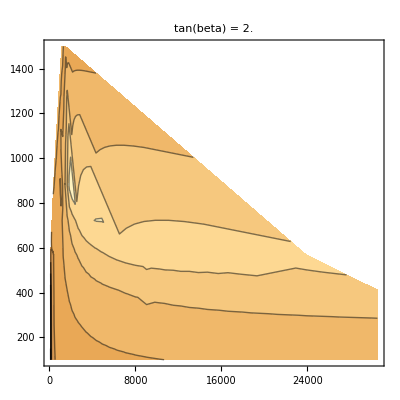

```mathematica
ListContourPlot[Cases[cleanData,{ms_,ma2_,tanBetaPoints[[1]],mh_}:>{ms,Sqrt[ma2],mh}],PlotLabel->"tan(beta) = " <> ToString[tanBetaPoints[[1]]]]
```

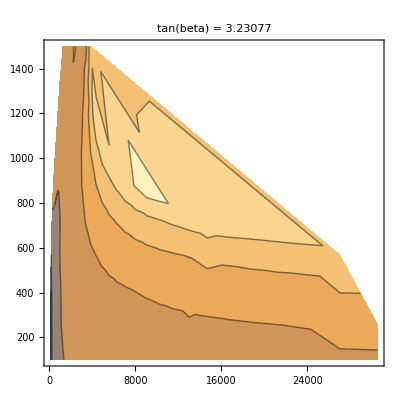

```mathematica
ListContourPlot[Cases[cleanData,{ms_,ma2_,tanBetaPoints[[2]],mh_}:>{ms,Sqrt[ma2],mh}],PlotLabel->"tan(beta) = " <> ToString[tanBetaPoints[[2]]]]
```

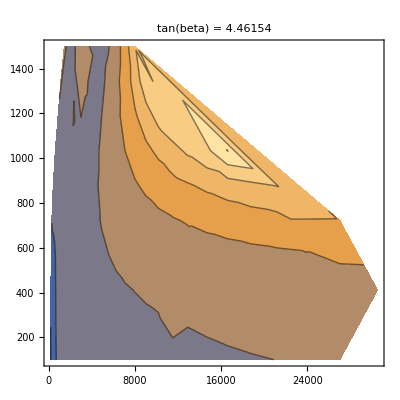

```mathematica
ListContourPlot[Cases[cleanData,{ms_,ma2_,tanBetaPoints[[3]],mh_}:>{ms,Sqrt[ma2],mh}],PlotLabel->"tan(beta) = " <> ToString[tanBetaPoints[[3]]]]
```

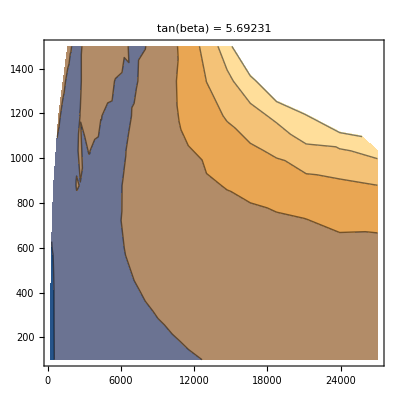

```mathematica
ListContourPlot[Cases[cleanData,{ms_,ma2_,tanBetaPoints[[4]],mh_}:>{ms,Sqrt[ma2],mh}],PlotLabel->"tan(beta) = " <> ToString[tanBetaPoints[[4]]]]
```

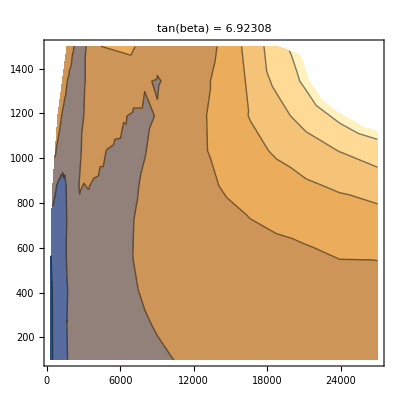

```mathematica
ListContourPlot[Cases[cleanData,{ms_,ma2_,tanBetaPoints[[5]],mh_}:>{ms,Sqrt[ma2],mh}],PlotLabel->"tan(beta) = " <> ToString[tanBetaPoints[[5]]]]
```

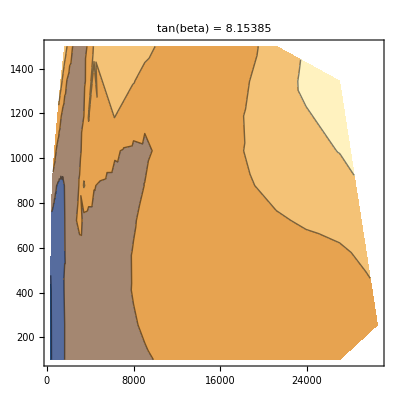

```mathematica
ListContourPlot[Cases[cleanData,{ms_,ma2_,tanBetaPoints[[6]],mh_}:>{ms,Sqrt[ma2],mh}],PlotLabel->"tan(beta) = " <> ToString[tanBetaPoints[[6]]]]
```

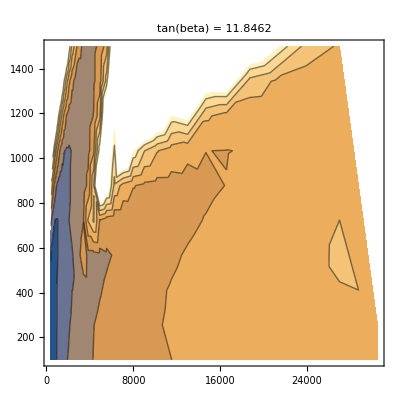

```mathematica
ListContourPlot[Cases[cleanData,{ms_,ma2_,tanBetaPoints[[9]],mh_}:>{ms,Sqrt[ma2],mh}],PlotLabel->"tan(beta) = " <> ToString[tanBetaPoints[[9]]]]
```

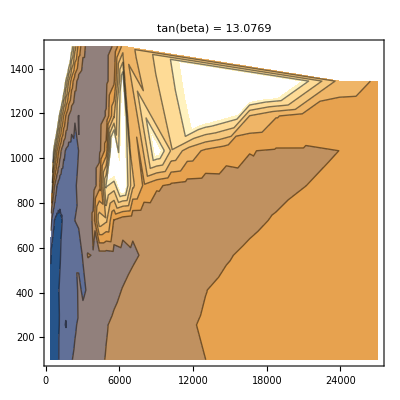

```mathematica
ListContourPlot[Cases[cleanData,{ms_,ma2_,tanBetaPoints[[10]],mh_}:>{ms,Sqrt[ma2],mh}],PlotLabel->"tan(beta) = " <> ToString[tanBetaPoints[[10]]]]
```

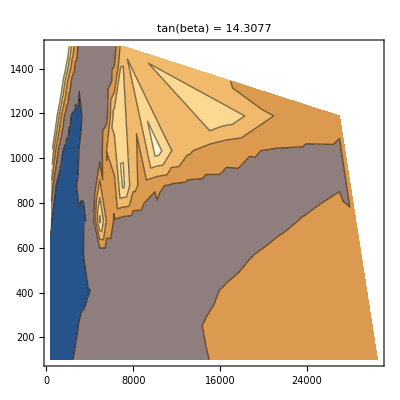

```mathematica
ListContourPlot[Cases[cleanData,{ms_,ma2_,tanBetaPoints[[11]],mh_}:>{ms,Sqrt[ma2],mh}],PlotLabel->"tan(beta) = " <> ToString[tanBetaPoints[[11]]]]
```

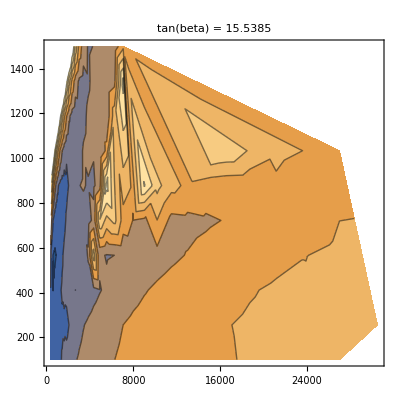

```mathematica
ListContourPlot[Cases[cleanData,{ms_,ma2_,tanBetaPoints[[12]],mh_}:>{ms,Sqrt[ma2],mh}],PlotLabel->"tan(beta) = " <> ToString[tanBetaPoints[[12]]]]
```

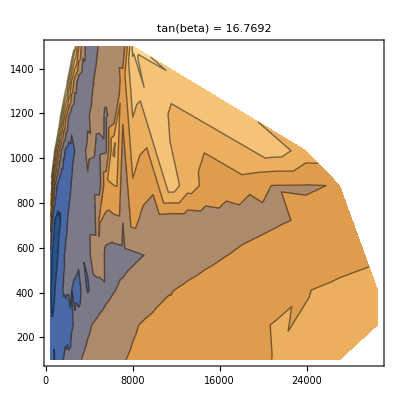

```mathematica
ListContourPlot[Cases[cleanData,{ms_,ma2_,tanBetaPoints[[13]],mh_}:>{ms,Sqrt[ma2],mh}],PlotLabel->"tan(beta) = " <> ToString[tanBetaPoints[[13]]]]
```

```mathematica
ListContourPlot[Cases[cleanData,{ms_,ma2_,tanBetaPoints[[4]],mh_}:>{ms,Sqrt[ma2],mh}],PlotLabel->"tan(beta) = " <> ToString[tanBetaPoints[[4]]]]
```

-Graphics-

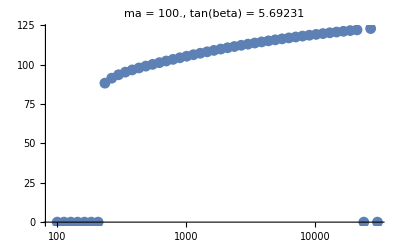

```mathematica
ListLogLinearPlot[Cases[data,{ms_,ma2Points[[1]],tanBetaPoints[[4]],mh_}:>{ms,mh}],PlotLabel->"ma = "<>ToString[Sqrt[ma2Points[[1]]]]<>", tan(beta) = " <> ToString[tanBetaPoints[[4]]]]
```

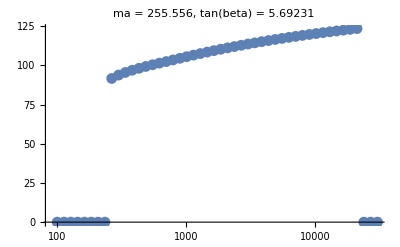

```mathematica
ListLogLinearPlot[Cases[data,{ms_,ma2Points[[2]],tanBetaPoints[[4]],mh_}:>{ms,mh}],PlotLabel->"ma = "<>ToString[Sqrt[ma2Points[[2]]]]<>", tan(beta) = " <> ToString[tanBetaPoints[[4]]]]
```

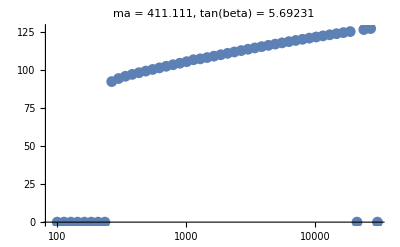

```mathematica
ListLogLinearPlot[Cases[data,{ms_,ma2Points[[3]],tanBetaPoints[[4]],mh_}:>{ms,mh}],PlotLabel->"ma = "<>ToString[Sqrt[ma2Points[[3]]]]<>", tan(beta) = " <> ToString[tanBetaPoints[[4]]]]
```

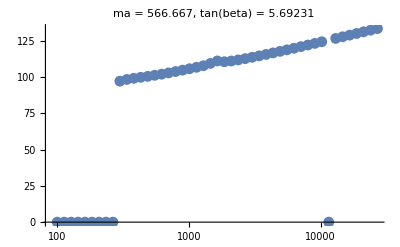

```mathematica
ListLogLinearPlot[Cases[data,{ms_,ma2Points[[4]],tanBetaPoints[[4]],mh_}:>{ms,mh}],PlotLabel->"ma = "<>ToString[Sqrt[ma2Points[[4]]]]<>", tan(beta) = " <> ToString[tanBetaPoints[[4]]]]
```

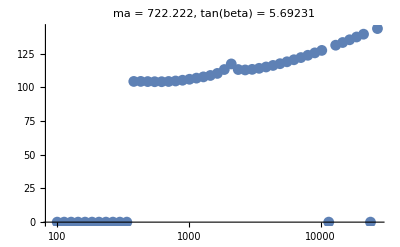

```mathematica
ListLogLinearPlot[Cases[data,{ms_,ma2Points[[5]],tanBetaPoints[[4]],mh_}:>{ms,mh}],PlotLabel->"ma = "<>ToString[Sqrt[ma2Points[[5]]]]<>", tan(beta) = " <> ToString[tanBetaPoints[[4]]]]
```

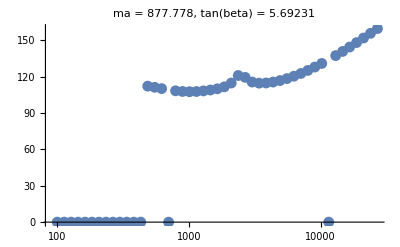

```mathematica
ListLogLinearPlot[Cases[data,{ms_,ma2Points[[6]],tanBetaPoints[[4]],mh_}:>{ms,mh}],PlotLabel->"ma = "<>ToString[Sqrt[ma2Points[[6]]]]<>", tan(beta) = " <> ToString[tanBetaPoints[[4]]]]
```

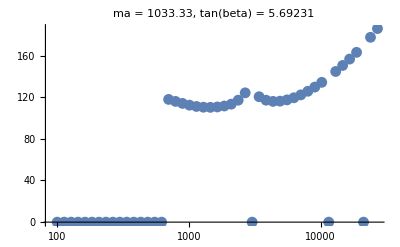

```mathematica
ListLogLinearPlot[Cases[data,{ms_,ma2Points[[7]],tanBetaPoints[[4]],mh_}:>{ms,mh}],PlotLabel->"ma = "<>ToString[Sqrt[ma2Points[[7]]]]<>", tan(beta) = " <> ToString[tanBetaPoints[[4]]]]
```

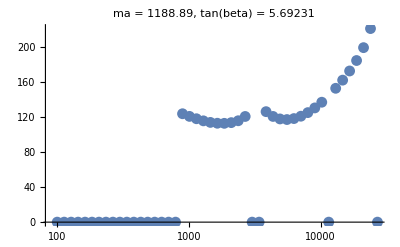

```mathematica
ListLogLinearPlot[Cases[data,{ms_,ma2Points[[8]],tanBetaPoints[[4]],mh_}:>{ms,mh}],PlotLabel->"ma = "<>ToString[Sqrt[ma2Points[[8]]]]<>", tan(beta) = " <> ToString[tanBetaPoints[[4]]]]
```

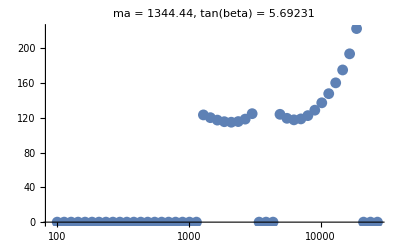

```mathematica
ListLogLinearPlot[Cases[data,{ms_,ma2Points[[9]],tanBetaPoints[[4]],mh_}:>{ms,mh}],PlotLabel->"ma = "<>ToString[Sqrt[ma2Points[[9]]]]<>", tan(beta) = " <> ToString[tanBetaPoints[[4]]]]
```

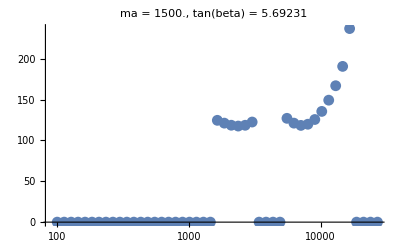

```mathematica
ListLogLinearPlot[Cases[data,{ms_,ma2Points[[10]],tanBetaPoints[[4]],mh_}:>{ms,mh}],PlotLabel->"ma = "<>ToString[Sqrt[ma2Points[[10]]]]<>", tan(beta) = " <> ToString[tanBetaPoints[[4]]]]
```